High-symmetry tetragonal antiferromagnet: spin symmetry and SOC

Consider the tetragonal antiferromagnet with magnetic space group 124.360, P_c4/mcc. Its 32 operations generate two sites, at z=0 and z=1/2, with opposite moments. We compare the Hamiltonians and bands with and without spin-orbit coupling (SOC). Keep all px, py, and pz spin states so that onsite SOC can mix the different orbitals and spins.

```mathematica
Needs["MagneticTB`"]
```

High-symmetry MSG 124.360 with SOC

With SOC, spin rotates together with the spatial operation. Pass the complete magnetic space group to init, then calculate the onsite term and the nearest-neighbor hopping between the two layers:

```mathematica
init[
  lattice -> DiagonalMatrix[{a, a, c}],
  lattpar -> {a -> 1, c -> 3/2},
  wyckoffposition -> {{{0, 0, 0}, {0, 0, 1}}},
  symminformation -> msgop[typeIV[{124, 360}]],
  basisFunctions -> {{
    "pxup", "pxdn", "pyup", "pydn", "pzup", "pzdn"
  }},
  InitialBondShells -> 2
];
socHamiltonian = symham[1] + symham[2];
socRepresentation = CurrentModelSession[][
  "FullRepresentation", "RepresentationMatrices"
];
```

```mathematica
showCrystalStructure[]
```

-Graphics3D-

The two layers have opposite moments. The 6 by 6 matrix below is the onsite block of the z=0 layer, with rows and columns ordered as {pxup,pxdn,pyup,pydn,pzup,pzdn}:

```mathematica
MatrixForm[symham[1][[1 ;; 6, 1 ;; 6]]]
```

(-e8 | 0 | ⅈ e4 | 0 | 0 | -e1
0 | -e7 | 0 | ⅈ e3 | e2 | 0
-ⅈ e4 | 0 | -e8 | 0 | 0 | ⅈ e1
0 | -ⅈ e3 | 0 | -e7 | ⅈ e2 | 0
0 | e2 | 0 | -ⅈ e2 | -e6 | 0
-e1 | 0 | -ⅈ e1 | 0 | 0 | -e5)

Without SOC: add continuous C-infinity spin symmetry

Without SOC, spin can also rotate independently about the magnetic axis. Write the finite operations as a spin-space group and add this continuous C_infinity symmetry. The finite representation matrices below come from the preceding model; pass them to initfromrep together with the continuous rotation.

```mathematica
initfromrep[
  lattice -> DiagonalMatrix[{a, a, c}],
  lattpar -> {a -> 1, c -> 3/2},
  wyckoffposition -> {{{0, 0, 0}, {0, 0, 1}}},
  symminformation -> Append[
    Association @ MapIndexed[
      "g" <> ToString[#2[[1]]] -> <|
        "space" -> #1[[{2, 3}]],
        "spin" -> {
          Det[#1[[2]]] #1[[2]], Boole[#1[[4]] == "T"]
        }
      |> &,
      msgop[typeIV[{124, 360}]]
    ],
    "C_infty" -> <|
      "space" -> {IdentityMatrix[3], {0, 0, 0}},
      "spin" -> {{
        {Cos[theta], -Sin[theta], 0},
        {Sin[theta], Cos[theta], 0},
        {0, 0, 1}
      }, 0},
      "continuous" -> theta
    |>
  ],
  repinformation -> <|
    "Discrete" -> {MapThread[
      Function[{matrix, operation},
        With[{site = First@FirstPosition[
            First@CurrentModelSession[][
              "ModelSpecification", "SiteOrbits"
            ],
            Mod[operation[[3]], 1]
          ]},
          matrix[[6 (site - 1) + Range[6], Range[6]]]
        ]
      ],
      {socRepresentation, msgop[typeIV[{124, 360}]]}
    ]},
    "Continuous" -> <|
      "SiteMatrices" -> {ConstantArray[
        KroneckerProduct[
          IdentityMatrix[3],
          DiagonalMatrix[{Exp[-I theta/2], Exp[I theta/2]}]
        ],
        2
      ]}
    |>
  |>,
  orbitalLabels -> {{
    "pxup", "pxdn", "pyup", "pydn", "pzup", "pzdn"
  }},
  InitialBondShells -> 2
];
noSOCHamiltonian = symham[1] + symham[2];
```

```mathematica
MatrixForm[symham[1][[1 ;; 6, 1 ;; 6]]]
```

(e1 | 0 | ⅈ e5 | 0 | 0 | 0
0 | e2 | 0 | ⅈ e6 | 0 | 0
-ⅈ e5 | 0 | e1 | 0 | 0 | 0
0 | -ⅈ e6 | 0 | e2 | 0 | 0
0 | 0 | 0 | 0 | e3 | 0
0 | 0 | 0 | 0 | 0 | e4)

Compare the two onsite matrices. C_infinity sets the px/py-pz spin-mixing terms to zero. With onsite and nearest-neighbor hopping retained, the numbers of real parameters are 13 with SOC and 9 without SOC:

```mathematica
{
  Length[Variables[socHamiltonian]],
  Length[Variables[noSOCHamiltonian]]
}
```

{13,9}

Band splitting along G-Z

The nearest neighbors lie along c, so plot the bands on G-Z. For clarity, keep one nonzero hopping parameter in each model. In the SOC model, also turn on the two onsite spin-orbital mixing terms shown in the matrix above.

The bands with SOC are:

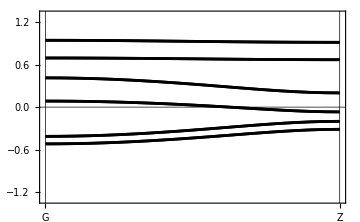

```mathematica
bandplot[
  {{{{0, 0, 0}, {0, 0, 1/2}}, {"G", "Z"}}},
  20,
  socHamiltonian /. Thread[
    {e1, e2, e3, e4, e5, e6, e7, e8, t1, t2, t3, t4, t5} ->
    {0.25, 0.25, 0, 0, -0.8, -0.4, -0.2, 0.2, -0.18, 0, 0, 0, 0}
  ],
  {},
  plotRange -> {-1.3, 1.3}, FontSize -> 18, ImageSize -> 360
]
```

With C_infinity symmetry and no SOC, the bands are:

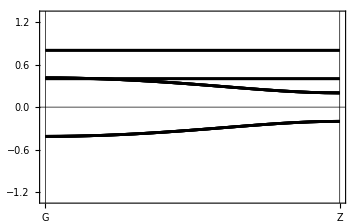

```mathematica
bandplot[
  {{{{0, 0, 0}, {0, 0, 1/2}}, {"G", "Z"}}},
  20,
  noSOCHamiltonian /. Thread[
    {e1, e2, e3, e4, e5, e6, t1, t2, t3} ->
    {-0.2, 0.2, 0.4, 0.8, 0, 0, -0.18, 0, 0}
  ],
  {},
  plotRange -> {-1.3, 1.3}, FontSize -> 18, ImageSize -> 360
]
```

For these parameter values, the SOC model has six doubly degenerate levels at G. Without SOC, the degeneracies at G are {4,2,4,2}. The fourfold degeneracies occur at this high-symmetry point; they do not extend along the whole path.

Scope of the continuous interface

The continuous operation used by initfromrep is one pure spin C_infinity rotation with no spatial action. Supply the complete finite group and its matrices in matching order. This rotation restricts the local states; it does not generate more atoms, complete the finite group, or add neighbor hoppings.

typeIV ▪ init ▪ initfromrep ▪ symham ▪ bandplot ▪ showCrystalStructure ▪ MagneticTB

History